```mathematica
a={-2 x[t],-2 y[t]-z[t],y[t]};
b={-2 x[t] z[t],-2 y[t] z[t],-2 (-1+z[t]^2)};
initial={0,0,1};
ito=ItoProcess[{a,b},{{x,y,z},initial},t];
stra=StratonovichProcess@ito;
ndEqs=Join[Thread[D[{x[t],y[t],z[t]},t]==a],Thread[{x[0],y[0],z[0]}==initial]];
nonRandomSol=NDSolveValue[ndEqs,{x,y,z},{t,0,10}];
```

```mathematica
trajIto=RandomFunction[ito,{0,10,.001},100];
trajStra=RandomFunction[stra,{0,10,.001},100];
meanIto=Transpose[Mean@trajIto["ValueList"]];
meanStra=Transpose[Mean@trajStra["ValueList"]];
```

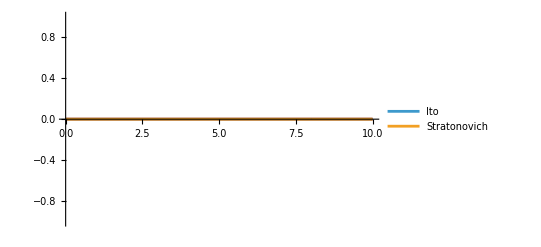
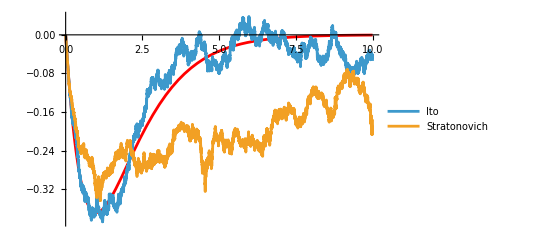
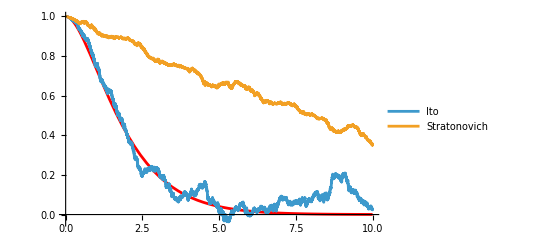

```mathematica
Table[Show[Plot[nonRandomSol[[j]][t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[{meanIto[[j]],meanStra[[j]]},PlotRange->All,DataRange->{0,10},PlotLegends->{"Ito","Stratonovich"}]],{j,3}]
```